## 1 Import demand datasets

```mathematica
(*All datasets should be stored in a folder called "DataDir".*)
SetDirectory[FileNameJoin[{NotebookDirectory[],"DataDir"}]];
```

```mathematica
monthlyTotalDemand09to23=Import["exp_monthly_total_demand09to23.csv"];
monthlyTotalDemandTS=TimeSeries[ToExpression[#]&/@monthlyTotalDemand09to23]
```

TimeSeries[…]

## 2 Extract trend with non-parametric smoothing technique

### 2.1 Methods

#### 2.1.1 Arithmetic mean 12

```mathematica
demand2009A=Log[monthlyTotalDemandTS["Values"]][[;;12]];
```

Left overhang and the year 2009 is used as padding.

```mathematica
trendMean12A=ListConvolve[ConstantArray[1,12]/12,Log[monthlyTotalDemandTS],1,demand2009A]
```

TimeSeries[…]

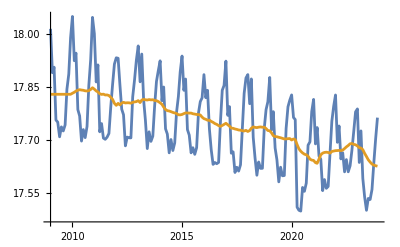

```mathematica
ListLinePlot[{Log[monthlyTotalDemandTS],trendMean12A}]
```

#### 2.1.2 Arithmetic mean 24

```mathematica
demand2009and2010A=Log[monthlyTotalDemandTS["Values"]][[;;24]];
```

Left overhang and the year 2009 is used as padding.

```mathematica
trendMean24A=ListConvolve[ConstantArray[1,24]/24,Log[monthlyTotalDemandTS],1,demand2009and2010A]
```

TimeSeries[…]

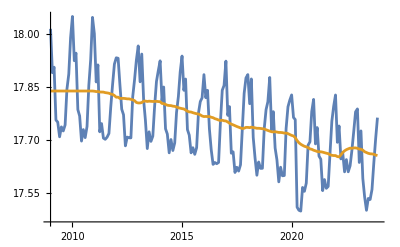

```mathematica
ListLinePlot[{Log[monthlyTotalDemandTS],trendMean24A}]
```

#### 2.1.3 Low pass Gaussian filter kernel = 12 months

We reach similar smoothing between box filter of radius r (i.e. arithmetic mean) and gaussian filter of radius 2r.

```mathematica
trendGaussian12A=GaussianFilter[Log[monthlyTotalDemandTS],12,Padding->"Reflected"]
```

TimeSeries[…]

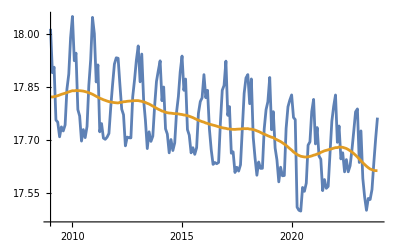

```mathematica
ListLinePlot[{Log[monthlyTotalDemandTS],trendGaussian12A}]
```

#### 2.1.3 Low pass Gaussian filter kernel = 24 months

We reach similar smoothing between box filter of radius r (i.e. arithmetic mean) and gaussian filter of radius 2r.

```mathematica
trendGaussian24A=GaussianFilter[Log[monthlyTotalDemandTS],24,Padding->"Reflected"]
```

TimeSeries[…]

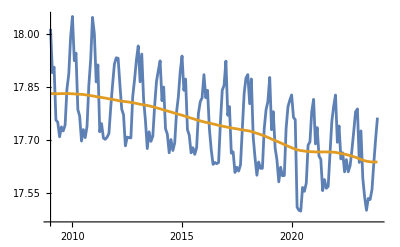

```mathematica
ListLinePlot[{Log[monthlyTotalDemandTS],trendGaussian24A}]
```

#### 2.1.4 Linearly decreasing weighted average

```mathematica
linearFunction[x_]:=Which[
x<12,x*1/12,
x>12,x*(-1/12)+2,
True,1
]
```

```mathematica
Through[{Dimensions,Total}[Array[linearFunction,24,0]]]
```

{{24},12}

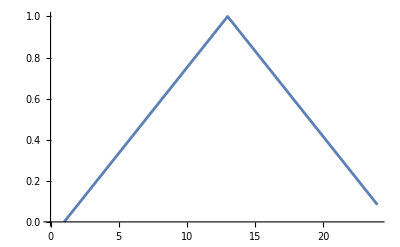

```mathematica
ListLinePlot[Array[linearFunction,24,0]]
```

```mathematica
trendLinearDecreaseA=ListConvolve[Array[linearFunction,24,0]/12,Log[monthlyTotalDemandTS],1,demand2009A]
```

TimeSeries[…]

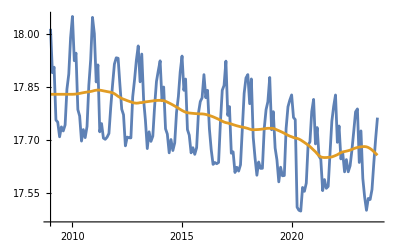

```mathematica
ListLinePlot[{Log[monthlyTotalDemandTS],trendLinearDecreaseA}]
```

### 2.2 Evaluation of goodness of fit and smoothness of the trend time series

#### 2.2.1 Goodness of fit

-Graphics-

-Graphics-

```mathematica
yearlyMeanA=Flatten[Table[Table[Mean[Log[monthlyTotalDemandTS["Values"]][[i;;i+12]]],12],{i,1,Length[monthlyTotalDemandTS["Values"]]/12}]];
```

```mathematica
overallMeanA=Mean[Log[monthlyTotalDemandTS["Values"]]]
```

17.7441

```mathematica
rSquaredMean12A=1-(Total[((Log[monthlyTotalDemandTS]-trendMean12A)^2)["Values"]]/Total[((Log[monthlyTotalDemandTS["Values"]]-yearlyMeanA)^2)]);
rSquaredMean24A=1-(Total[((Log[monthlyTotalDemandTS]-trendMean24A)^2)["Values"]]/Total[((Log[monthlyTotalDemandTS["Values"]]-yearlyMeanA)^2)]);
rSquaredGaussian12A=1-Total[((Log[monthlyTotalDemandTS]-trendGaussian12A)^2)["Values"]]/Total[((Log[monthlyTotalDemandTS["Values"]]-yearlyMeanA)^2)];
rSquaredGaussian24A=1-Total[((Log[monthlyTotalDemandTS]-trendGaussian24A)^2)["Values"]]/Total[((Log[monthlyTotalDemandTS["Values"]]-yearlyMeanA)^2)];
rSquaredLinearA=1-Total[((Log[monthlyTotalDemandTS]-trendLinearDecreaseA)^2)["Values"]]/Total[((Log[monthlyTotalDemandTS["Values"]]-yearlyMeanA)^2)];
```

```mathematica
MSEMean12A=Mean[((Log[monthlyTotalDemandTS]-trendMean12A)^2)["Values"]];
MSEMean24A=Mean[((Log[monthlyTotalDemandTS]-trendMean24A)^2)["Values"]];
MSEGaussian12A=Mean[((Log[monthlyTotalDemandTS]-trendGaussian12A)^2)["Values"]];
MSEGaussian24A=Mean[((Log[monthlyTotalDemandTS]-trendGaussian24A)^2)["Values"]];
MSELinearA=Mean[((Log[monthlyTotalDemandTS]-trendLinearDecreaseA)^2)["Values"]];
```

```mathematica
Grid[{{"","R squared","MSE"},
{"Arithmetic mean 12",
ResourceFunction["DecimalRound"][rSquaredMean12A,3],
ResourceFunction["DecimalRound"][MSEMean12A,3]},
{"Arithmetic mean 24",
ResourceFunction["DecimalRound"][rSquaredMean24A,3],
ResourceFunction["DecimalRound"][MSEMean24A,3]},
{"Gaussian LP filter, kernel=12",
ResourceFunction["DecimalRound"][rSquaredGaussian12A,3],
ResourceFunction["DecimalRound"][MSEGaussian12A,3]},
{"Gaussian LP filter, kernel=24",
ResourceFunction["DecimalRound"][rSquaredGaussian24A,3],
ResourceFunction["DecimalRound"][MSEGaussian24A,3]},
{"Linearly decreasing weights",
ResourceFunction["DecimalRound"][rSquaredLinearA,3],
ResourceFunction["DecimalRound"][MSELinearA,3]}}]
```

| R squared | MSE
Arithmetic mean 12 | 0.604 | 0.00945
Arithmetic mean 24 | 0.594 | 0.00969
Gaussian LP filter, kernel=12 | 0.613 | 0.00924
Gaussian LP filter, kernel=24 | 0.607 | 0.00938
Linearly decreasing weights | 0.584 | 0.00992

#### 2.2.1 Smoothness

-Graphics-

Digital Image Processing
 FOURTH EDITION
 Rafael C. Gonzalez • Richard E. Woods

-Graphics-

-Graphics-
Second derivative kernel: {1,-2,1}

```mathematica
smoothnessMean12A=Sqrt[Total[#]/Length[#]]&@((ListConvolve[{1,-2,1},trendMean12A])^2)["Values"];
smoothnessMean24A=Sqrt[Total[#]/Length[#]]&@((ListConvolve[{1,-2,1},trendMean24A])^2)["Values"];
smoothnessGaussian12A=Sqrt[Total[#]/Length[#]]&@((ListConvolve[{1,-2,1},trendGaussian12A])^2)["Values"];
smoothnessGaussian24A=Sqrt[Total[#]/Length[#]]&@((ListConvolve[{1,-2,1},trendGaussian24A])^2)["Values"];
smoothnessLinearDecreaseA=Sqrt[Total[#]/Length[#]]&@((ListConvolve[{1,-2,1},trendLinearDecreaseA])^2)["Values"];
```

```mathematica
Grid[{{"","Smoothness factor"},
{"Arithmetic mean 12",ResourceFunction["DecimalRound"][smoothnessMean12A,3]},
{"Arithmetic mean 24",ResourceFunction["DecimalRound"][smoothnessMean24A,3]},
{"Gaussian LP filter, kernel=12",ResourceFunction["DecimalRound"][smoothnessGaussian12A,3]},
{"Gaussian LP filter, kernel=24",ResourceFunction["DecimalRound"][smoothnessGaussian24A,3]},
{"Linearly decreasing weights",ResourceFunction["DecimalRound"][smoothnessLinearDecreaseA,3]}}]
```

| Smoothness factor
Arithmetic mean 12 | 0.0035
Arithmetic mean 24 | 0.00155
Gaussian LP filter, kernel=12 | 0.000788
Gaussian LP filter, kernel=24 | 0.0004
Linearly decreasing weights | 0.000515

We select the Gaussian LP filter as it has the highest R squared and a good smoothness.